```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
σ=0.00001;
```

```mathematica
SIGMA={{σ^2,0},{0,1}};
```

```mathematica
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
```

```mathematica
dU[x_,y_]=GradientG[U[x,y],{x,y}];
```

```mathematica
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

10013.607995.271740.5643690.5122780.9892794.59727796750.0.00001853880.000693433True{1,2}{4}

20021.41149×10^61.276220.2533550.2580311.01274.169711.41149×10^60.00001853880.000520987False{1}{3}

3003-0.1575733.900180.8109610.3215154.141663.984091.41149×10^60.00001853880.000762777True{1,2,3}{1,4}

40042.06655×10^63.584870.4327930.1114982.092664.51992.06656×10^60.00001853880.000391425False{1}{3}

5005-0.3931172.746331.0.4.575134.182012.27321×10^60.00001853880.000573086True{1,4}{1,4}

60062.2732×10^60.6755980.3539180.5602729.596644.182012.27321×10^60.00001853880.000573086False{1,4}{1,4}

70072.780863.219370.9556480.05037721.401154.182012.27321×10^60.00001853880.000573086True{1,4}{1,4}

80082.27321×10^60.9323340.6143560.3530951.695594.182012.27321×10^60.00001853880.000573086False{1,4}{1,4}

90092.562381.529410.602850.4258571.619634.182012.27321×10^60.00001853880.000573086True{1,4}{1,4}

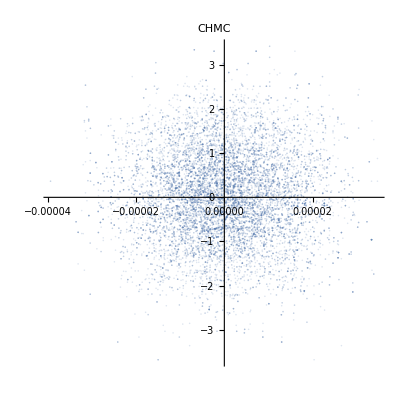

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True,{}];
ListPlot[QS,PlotLabel->CHMC,PlotStyle->Opacity[.2],AspectRatio->1]
```

```mathematica
StandardDeviation[QS]
```

{0.0000112712,0.99391}

10019.53674×10^-61.901142.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

20029.53674×10^-62.756652.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

30039.53674×10^-62.815312.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

40049.53674×10^-63.732842.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

50059.53674×10^-61.737742.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

60069.53674×10^-62.997462.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

70079.53674×10^-63.818022.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

80089.53674×10^-63.467662.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

90099.53674×10^-61.981212.06115×10^-90.1.36111×10^101.36111×10^102.72222×10^100.00001853880.01True{1}{3}

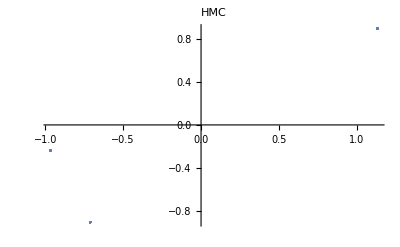

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False,{}];
ListPlot[QS,PlotLabel->HMC,PlotStyle->Opacity[.1]]
```

100133.46634.995970.6440340.5585490.7394612.50815×10^1034.20580.010.174494False{1,4}{1,4}

200267.9873.424730.7758830.2137463.129272.50815×10^1071.11630.010.0740025False{1}{4}

3003140.8421.062530.381520.4680041.465052.50815×10^10142.3070.010.0459497False{1}{4}

400477.48391.044220.5028440.4690650.91382.50815×10^1078.39770.010.14421False{1,4}{1,4}

5005406.561.241710.251890.3175164.857172.50815×10^10411.4180.010.0259374False{1}{4}

6006411.1043.131640.8003790.2831140.3135742.50815×10^10411.4180.010.0259374False{1}{4}

7007406.7412.160630.3538780.5596064.676252.50815×10^10411.4180.010.0259374False{1}{4}

8008409.9911.223470.5639470.2737831.426322.50815×10^10411.4180.010.0259374False{1}{4}

9009410.9660.1981410.7389510.2215430.4510962.50815×10^10411.4180.010.0259374False{1}{4}

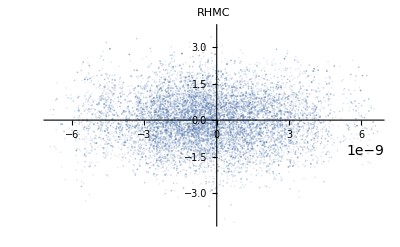

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,False,False,{}];
ListPlot[QS,PlotLabel->RHMC,PlotStyle->Opacity[.2]]
```